## Minima location in the Abs case

```mathematica
1/2 u^2+(y-Abs[√dq u+h])^2=1/2 u^2+(√dq u+h)^2+y^2-2y *Abs[√dq u+h]
```

Set::write: Tag Plus in u^2/2 + (y - Abs[h + Power[« 2 »]\ u])^2 is Protected.

u^2/2+(h+√dq u)^2+y^2-2 y Abs[h+√dq u]

True

```mathematica
FullSimplify[(1/2+dq)u^2+2 √dq h u-2y *Abs[√dq u+h]+h^2+y^2==1/2 u^2+(√dq u+h)^2+y^2-2y *Abs[√dq u+h]]
```

True

```mathematica
per u>-h/(√dq)-> h>-2 dq y
```

```mathematica
FullSimplify[(1/2+dq)u^2+2 √dq h u-2y (√dq u+h)+h^2+y^2==(1/2+dq)u^2+2 √dq(h -y)u-2y h+h^2+y^2]
```

True

```mathematica
D[(1/2+dq)u^2+2 √dq(h -y)u-2y h+h^2+y^2,u]
```

2 (1/2+dq) u+2 √dq (h-y)

```mathematica
Solve[2 (1/2+dq) u+2 √dq (h-y)==0,u]
```

```mathematica
{{u->-(2 √dq (h-y))/(1+2 dq)}}
Solve[-(2 √dq (h-y))/(1+2 dq)+h/(√dq)==0,h]
```

{{u→-(2 √dq (h-y))/(1+2 dq)}}

{{h→-2 dq y}}

```mathematica
per u<-h/(√dq)-> h<2dq y
```

```mathematica
FullSimplify[(1/2+dq)u^2+2 √dq h u+2y (√dq u+h)+h^2+y^2==(1/2+dq)u^2+2 √dq(h+y) u+2y h+h^2+y^2]
```

True

```mathematica
D[(1/2+dq)u^2+2 √dq(h+y) u+2y h+h^2+y^2,u]
```

2 (1/2+dq) u+2 √dq (h+y)

```mathematica
Solve[2 (1/2+dq) u+2 √dq (h+y)==0, u]
```

{{u→-(2 √dq (h+y))/(1+2 dq)}}

```mathematica
Solve[-(2 √dq (h+y))/(1+2 dq)+h/(√dq)==0,h]
```

{{h→2 dq y}}

```mathematica
D[1/2 u^2+(y-Abs[√dq u+h])^2,u]
```

```mathematica
Solve[u-2 √dq (y-Abs[h+√dq u]) Abs'[h+√dq u]==0,u]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[u-2 √dq (y-Abs[h+√dq u]) Abs'[h+√dq u]==0,u]

```mathematica
Manipulate[Show[Plot[{1/2 u^2+(y-Abs[√dq u+h])^2,If[Abs[h]>-2dq y,(Abs[h]-y)^2/(1+2 dq),1/2 h^2/dq+y^2]},{u,-10,10}],ListPlot[{{-(2 √dq (h+y))/(1+2 dq),0},{-(2 √dq (h+y))/(1+2 dq),200}},Joined->True,PlotStyle->Red],ListPlot[{{-(2 √dq (h-y))/(1+2 dq),0},{-(2 √dq (h-y))/(1+2 dq),200}},Joined->True,PlotStyle->Purple],ListPlot[{{-h/(√dq),0},{-h/(√dq),200}},Joined->True,PlotStyle->Black]],{y,-3,3},{dq,0,5},{h,-3,3}]
```

```mathematica
h<2dq y -> (h+y)^2/(1+2 dq), h>-2 dq y-> (h-y)^2/(1+2 dq)
```

```mathematica
1st root
```

```mathematica
(1/2+dq)u^2+2 √dq(h-y) u-2y h+h^2+y^2/.{u->-(2 √dq (h-y))/(1+2 dq)}
```

h^2+(4 dq (1/2+dq) (h-y)^2)/(1+2 dq)^2-(4 dq (h-y)^2)/(1+2 dq)-2 h y+y^2

```mathematica
Simplify[h^2+(4 dq (1/2+dq) (h-y)^2)/(1+2 dq)^2-(4 dq (h-y)^2)/(1+2 dq)-2 h y+y^2]
```

(h-y)^2/(1+2 dq)

```mathematica
2nd root
```

```mathematica
(1/2+dq)u^2+2 √dq(h+y) u+2y h+h^2+y^2/.{u->-(2 √dq (h+y))/(1+2 dq)}
```

```mathematica
Simplify[h^2+2 h y+y^2+(4 dq (1/2+dq) (h+y)^2)/(1+2 dq)^2-(4 dq (h+y)^2)/(1+2 dq)]
```

(h+y)^2/(1+2 dq)

```mathematica
3rd root
```

```mathematica
1/2 h^2/dq+y^2
```

```mathematica
Simplify[(h-y)^2/(1+2 dq)-(1/2 h^2/dq+y^2)]
```

-(h+2 dq y)^2/(2 dq (1+2 dq))

```mathematica
Simplify[(h+y)^2/(1+2 dq)-(1/2 h^2/dq+y^2)]
```

```mathematica
-(h-2 dq y)^2/(2 dq (1+2 dq))
Solve[(h-2 dq y)^2==0]
```

-(h-2 dq y)^2/(2 dq (1+2 dq))

{{h→2 dq y}}

```mathematica
Solve[(h-y)^2/(1+2 dq)-(1/2 h^2/dq+y^2)==0,h]
```

```mathematica
{{h->-2 dq y},{h->-2 dq y}}
```

```mathematica
Solve[(h+y)^2/(1+2 dq)-(1/2 h^2/dq+y^2)==0,h]
```

{{h→2 dq y},{h→2 dq y}}

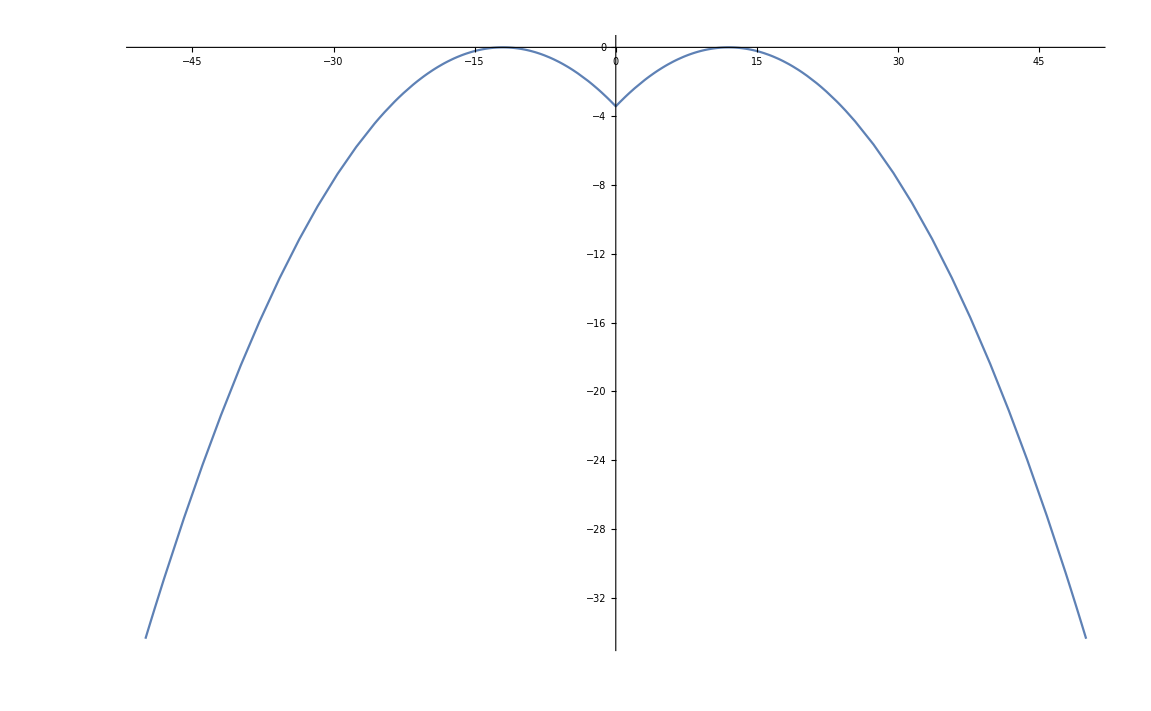

```mathematica
With[{y=-2.,dq=3.},Plot[(Abs[h]-y)^2/(1+2 dq)-1/2 h^2/dq-y^2,{h,-50,50}]]
```

## For the analytic computation of the Ge

```mathematica
Integrate[(ⅇ^(-z^2/2))/(√(2π)),{z,a,∞}]
```

1/2 Erfc[a/(√2)]

```mathematica
Integrate[z(ⅇ^(-z^2/2))/(√(2π)),{z,a,∞}]
```

(ⅇ^(-a^2/2))/(√(2 π))

```mathematica
Integrate[z^2(ⅇ^(-z^2/2))/(√(2π)),{z,a,∞}]
```

(a ⅇ^(-a^2/2))/(√(2 π))+1/2 Erfc[a/(√2)]

```mathematica
Integrate[z^2(ⅇ^(-z^2/2))/(√(2π)),{z,0,∞}]
```

1/2

```mathematica
Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-(c z+b)^2/2))/(√(2π))HeavisideTheta[c z+a],{z,-∞,∞}, Assumptions->{c>0}]
Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-(-c z+b)^2/2))/(√(2π))HeavisideTheta[-(c z+a)],{z,-∞,∞}, Assumptions->{c>0}]
```

(ⅇ^(-b^2/(2+2 c^2)) (1+Erf[(a+(a-b) c^2)/(√2 c √(1+c^2))]))/(2 √(1+c^2) √(2 π))

(ⅇ^(-b^2/(2+2 c^2)) Erfc[(a+(a+b) c^2)/(√2 c √(1+c^2))])/(2 √(1+c^2) √(2 π))

```mathematica
FullSimplify[Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-(c z+b)^2/2))/(√(2π))HeavisideTheta[c z+a],{z,-∞,∞}, Assumptions->{c>0}]+Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-(-c z+b)^2/2))/(√(2π))HeavisideTheta[-(c z+a)],{z,-∞,∞}, Assumptions->{c>0}]==(ⅇ^(-b^2/(2(1+ c^2))) (H[-(a+(a-b) c^2)/(c √(1+c^2))]+H[(a+(a+b) c^2)/(c √(1+c^2))]))/(√(1+c^2) √(2 π))]
```

True

```mathematica
Integrate[(ⅇ^(-z^2/2))/(√(2π))H[Abs[c z + a]+ b],{z,-∞,∞}, Assumptions->{c>0}]
```

Integrate[(ⅇ^(-z^2/2) Erfc[(b+Abs[z])/(√2)])/(2 √(2 π)),{z,-∞,∞},Assumptions→{c>0}]

```mathematica
Integrate[(z+a)(ⅇ^(-z^2/2))/(√(2π))HeavisideTheta[z+a],{z,-∞,∞}]
```

1/2 (a+ⅇ^(-a^2/2) √(2/π)+a Erf[a/(√2)])

```mathematica
Integrate[(-z-a)(ⅇ^(-z^2/2))/(√(2π))HeavisideTheta[-z-a],{z,-∞,∞}]
```

```mathematica
(ⅇ^(-a^2/2))/(√(2 π))-1/2 a Erfc[a/(√2)]
```

```mathematica
a1=√(Δ+(1-r^2/q0));b1 =r/√q0;c1=r/√q0*√(1/(1-r^2/q0)+1/Δ);d1=√((1-r^2/q0)/Δ);x1=√((q0-r^2+q0 Δ)/(q0+r^2 (-1+Δ)));x2=-(r Δ)/(√(q0+r^2 (-1+Δ)));x3=r √((q0-r^2+q0 Δ)/(q0+r^2 (-1+Δ)));x4=(q0-r^2)/(√(q0+r^2 (-1+Δ)));
```

```mathematica
Integrate[(ⅇ^(-y^2/2))/(√(2π))(a z0+b y-(c z0+d y))^2/(1-2dq)HeavisideTheta[c z0+d y+2dq (a z0+b y)],{y,-∞,∞},Assumptions->{dq>0,z0∈Reals,a>0,b<0,r>0,c>0,d>0}]
```

$Aborted

```mathematica
Integrate[(ⅇ^(-y^2/2))/(√(2π))(x1 z0+x2 y-Abs[x3 z0+x4 y])^2/(1-2dq)HeavisideTheta[Abs[x3 z0+x4 y]+2dq (x1 z0+x2 y)],{y,-∞,∞},Assumptions->{dq>0,z0<0,r^2/q0<1,Δ>0,r>0,q0>0}]
```

```mathematica
Integrate[(ⅇ^(-y^2/2))/(√(2π))HeavisideTheta[-(x3*z0+x4*y)]HeavisideTheta[-(x3*z0+x4*y)+2dq (x1*z0+x2*y)],{y,-∞,∞},Assumptions->{dq>0,z0∈Reals,r^2/q0<1,Δ>0,r>0,q0>0}]
```

1/2 (1+Erf[((-2 dq+r) z0 √(q0-r^2+q0 Δ))/(√2 (-q0+r^2-2 dq r Δ))]-(Erf[(r z0 √(q0-r^2+q0 Δ))/(√2 (q0-r^2))]+Erf[((-2 dq+r) z0 √(q0-r^2+q0 Δ))/(√2 (-q0+r^2-2 dq r Δ))]) HeavisideTheta[(dq z0 (q0+r^2 (-1+Δ)) √(q0-r^2+q0 Δ))/((q0-r^2) (q0-r (r-2 dq Δ)))])

```mathematica
Module[{q0=0.8,r=0.5,dq=1.4,Δ=0.5,z0=0.1},x1=√((q0-r^2+q0 Δ)/(q0+r^2 (-1+Δ)));x2=-(r Δ)/(√(q0+r^2 (-1+Δ)));x3=r √((q0-r^2+q0 Δ)/(q0+r^2 (-1+Δ)));x4=(q0-r^2)/(√(q0+r^2 (-1+Δ)));{N[1/2 (1+Erf[((2 dq x1+x3) z0)/(√2 (2 dq x2+x4))]+(Erf[(x3 z0)/(√2 x4)]-Erf[((2 dq x1+x3) z0)/(√2 (2 dq x2+x4))]) HeavisideTheta[(dq (-x2 x3+x1 x4) z0)/(x4 (2 dq x2+x4))])+1/2 (1+Erf[((2 dq x1-x3) z0)/(√2 (2 dq x2-x4))]+(Erf[(x3 z0)/(√2 x4)]-Erf[((2 dq x1-x3) z0)/(√2 (2 dq x2-x4))]) HeavisideTheta[-(dq (x2 x3-x1 x4) z0)/(x4 (2 dq x2-x4))])],NIntegrate[(ⅇ^(-y^2/2))/(√(2π))HeavisideTheta[Abs[x3*z0+x4*y]+2dq (x1*z0+x2*y)],{y,-∞,∞}]}]
```

{0.44484,0.983948}

```mathematica
FullSimplify[(ⅇ^(-a^2/2))/(√(2 π))-1/2 a Erfc[a/(√2)]+1/2 (a+ⅇ^(-a^2/2) √(2/π)+a Erf[a/(√2)]),Assumptions->{a>0}]
```

ⅇ^(-a^2/2) √(2/π)+a Erf[a/(√2)]

```mathematica
FullSimplify[ⅇ^(-a^2/2) √(2/π)+a Erf[a/(√2)]==ⅇ^(-a^2/2) √(2/π)+a (1-Erfc[a/(√2)]),Assumptions->a>0]
```

True

```mathematica
H[x_]:=1/2 Erfc[x/(√2)]
```

```mathematica
FullSimplify[ⅇ^(-a^2/2) √(2/π)+a Erf[a/(√2)]==ⅇ^(-a^2/2) √(2/π)+a (2H[-a]-1),Assumptions->a>0]
```

True

```mathematica
Integrate[Abs[z](ⅇ^(-z^2/2))/π ⅇ^(-(a^2 z^2)/2),{z,-∞,∞}]
```

Piecewise[{{2/((1+a^2) π), Re[a^2]>-1}, {Integrate[(ⅇ^(-z^2/2-(a^2 z^2)/2) Abs[z])/π,{z,-∞,∞},Assumptions→Re[a^2]≤-1], True}}]

```mathematica
Integrate[-z(ⅇ^(-z^2/2))/π ⅇ^(-(a^2 z^2)/2)HeavisideTheta[-z],{z,-∞,∞}]
```

ConditionalExpression[1/((1+a^2) π),Re[a^2]>-1]

```mathematica
With[{a=-0.2},{NIntegrate[z^2(ⅇ^(-z^2/2))/(√(2π)) H[-a z],{z,0,∞}],1-(1/(2π)ArcCot[a]-a/(2π(1+a^2)))}]
```

{0.187977,1.18798}

```mathematica
ArcCot[-1.2]
```

-0.694738

```mathematica
With[{a=0.2},{NIntegrate[Abs[z]z(ⅇ^(-z^2/2))/(√(2π)) H[-a z],{z,-∞,∞}],NIntegrate[z^2(ⅇ^(-z^2/2))/(√(2π)) (1-2H[a z]),{z,0,∞}],1/2-(1/π ArcCot[a]-a/(π(1+a^2)))}]
```

{0.124046,0.124046,0.124046}

```mathematica
Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-m(c z+a-y)^2/(1+2 dq)))/(√(2π))HeavisideTheta[c z+a],{z,-∞,∞},Assumptions->{c>0,dq>0,m>0}]
```

1/2 ⅇ^(-(m (a-y)^2)/(1+2 dq+2 c^2 m)) √((1+2 dq)/(2 π+4 dq π+4 c^2 m π)) (1+Erf[(a+2 a dq+2 c^2 m y)/(c √((2+4 dq) (1+2 dq+2 c^2 m)))])

```mathematica
Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-m(c z+a+y)^2/(1+2 dq)))/(√(2π))HeavisideTheta[-c z-a],{z,-∞,∞},Assumptions->{c>0,dq>0,m>0}]
```

1/2 ⅇ^(-(m (a+y)^2)/(1+2 dq+2 c^2 m)) √((1+2 dq)/(2 π+4 dq π+4 c^2 m π)) Erfc[(a+2 a dq-2 c^2 m y)/(c √((2+4 dq) (1+2 dq+2 c^2 m)))]

```mathematica
asd= ⅇ^(-(m (a-y)^2)/(1+2 dq+2 c^2 m)) √((1+2 dq)/(2 π+4 dq π+4 c^2 m π)) (H[-(a(1+2dq)+2 c^2 m y)/(c √((1+2 dq) (1+2 dq+2 c^2 m)))])+ ⅇ^(-(m (a+y)^2)/(1+2 dq+2 c^2 m)) √((1+2 dq)/(2 π+4 dq π+4 c^2 m π)) H[(a(1+2dq)-2 c^2 m y)/(c √((1+2dq) (1+2 dq+2 c^2 m)))]
```

```mathematica
Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-m(c z+a-y)^2/(1+2 dq)))/(√(2π))HeavisideTheta[c z+a]HeavisideTheta[c z+a+2dq y],{z,-∞,∞},Assumptions->{c>0,dq>0,m>0}]
```

1/(2 π)ⅇ^(-(m (a-y)^2)/(1+2 dq+2 c^2 m)) √((π+2 dq π)/(2+4 dq+4 c^2 m)) (1/(Abs[a-y] Abs[a+2 (dq+c^2 m) y])((-a+y) Abs[a+2 (dq+c^2 m) y] Erf[(√2 c m Abs[a-y])/(√((1+2 dq) (1+2 dq+2 c^2 m)))]+Abs[a-y] (Abs[a+2 (dq+c^2 m) y] (-1+Erf[(√2 c m (a-y))/(√((1+2 dq) (1+2 dq+2 c^2 m)))])-(a+2 (dq+c^2 m) y) Erf[(√((1+2 dq)/(2+4 dq+4 c^2 m)) Abs[a 2 (dq+c^2 m) y])/c])) (-1+HeavisideTheta[(2 dq y)/c])+(1+Erf[(a+2 a dq+2 c^2 m y)/(√2 c √((1+2 dq) (1+2 dq+2 c^2 m)))]) HeavisideTheta[(2 dq y)/c])

```mathematica
Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-m(c z+a+y)^2/(1+2 dq)))/(√(2π))HeavisideTheta[-(c z+a)]HeavisideTheta[-(c z+a)+2dq y],{z,-∞,∞},Assumptions->{c>0,dq>0,m>0}]
```

1/(2 π)ⅇ^(-(m (a+y)^2)/(1+2 dq+2 c^2 m)) √((π+2 dq π)/(2+4 dq+4 c^2 m)) (-1/(Abs[a+y] Abs[a-2 (dq+c^2 m) y])(-(a+y) Abs[a-2 (dq+c^2 m) y] Erf[(√2 c m Abs[a+y])/(√((1+2 dq) (1+2 dq+2 c^2 m)))]+Abs[a+y] (Abs[a-2 (dq+c^2 m) y] (1+Erf[(√2 c m (a+y))/(√((1+2 dq) (1+2 dq+2 c^2 m)))])+(-a+2 (dq+c^2 m) y) Erf[(√((1+2 dq)/(2+4 dq+4 c^2 m)) Abs[a-2 (dq+c^2 m) y])/c])) (-1+HeavisideTheta[(2 dq y)/c])+(1+Erf[(√2 c m (a+y))/(√((1+2 dq) (1+2 dq+2 c^2 m)))]-((a+y) Erf[(√2 c m Abs[a+y])/(√((1+2 dq) (1+2 dq+2 c^2 m)))])/Abs[a+y]-((a+2 a dq-2 c^2 m y) Erf[Abs[a+2 a dq-2 c^2 m y]/(√2 c √((1+2 dq) (1+2 dq+2 c^2 m)))])/(c (1+2 dq+2 c^2 m) Abs[a/c-(2 c m (a+y))/(1+2 dq+2 c^2 m)])) HeavisideTheta[(2 dq y)/c])

```mathematica
With[{a=1.1,dq=2.21,c=1.2,y=-0.5, m=2.1},{N[(ⅇ^(-(m (a-y)^2)/(1+2 dq+2 c^2 m)))/(√(2π(1+2 c^2 m/(1+2 dq )))) ( H[-(a+2 (dq+c^2 m) y)/(c √(1+2 c^2 m/(1+2 dq )))] (1-HeavisideTheta[ y])+H[-(a+2 a dq+2 c^2 m y)/(c √((1+2 dq) (1+2 dq+2 c^2 m)))] HeavisideTheta[ y])],N[1/(2 π)ⅇ^(-(m (a-y)^2)/(1+2 dq+2 c^2 m)) √((π+2 dq π)/(2+4 dq+4 c^2 m)) (1/(Abs[a-y] Abs[a+2 (dq+c^2 m) y])((-a+y) Abs[a+2 (dq+c^2 m) y] Erf[(√2 c m Abs[a-y])/(√((1+2 dq) (1+2 dq+2 c^2 m)))]+Abs[a-y] (Abs[a+2 (dq+c^2 m) y] (-1+Erf[(√2 c m (a-y))/(√((1+2 dq) (1+2 dq+2 c^2 m)))])-(a+2 (dq+c^2 m) y) Erf[(√((1+2 dq)/(2+4 dq+4 c^2 m)) Abs[a+2 (dq+c^2 m) y])/c])) (-1+HeavisideTheta[(2 dq y)/c])+(1+Erf[(a+2 a dq+2 c^2 m y)/(√2 c √((1+2 dq) (1+2 dq+2 c^2 m)))]) HeavisideTheta[(2 dq y)/c])]}]
```

{0.00153327,0.00153327}

```mathematica
With[{a=1.1,dq=2.21,c=1.2,y=-0.1, m=1.1},{N[(ⅇ^(-(m (a+y)^2)/(1+2 dq+2 c^2 m)))/(√(2π(1+2 c^2 m/(1+2 dq )))) (H[(a-2 (dq+c^2 m) y)/(c √(1+2 c^2 m/(1+2 dq )))] (1-HeavisideTheta[y])+(H[(a+2 a dq-2 c^2 m y)/(c √((1+2 dq) (1+2 dq+2 c^2 m)))]) HeavisideTheta[y])],N[1/(2 π)ⅇ^(-(m (a+y)^2)/(1+2 dq+2 c^2 m)) √((π+2 dq π)/(2+4 dq+4 c^2 m)) (-1/(Abs[a+y] Abs[a-2 (dq+c^2 m) y])(-(a+y) Abs[a-2 (dq+c^2 m) y] Erf[(√2 c m Abs[a+y])/(√((1+2 dq) (1+2 dq+2 c^2 m)))]+Abs[a+y] (Abs[a-2 (dq+c^2 m) y] (1+Erf[(√2 c m (a+y))/(√((1+2 dq) (1+2 dq+2 c^2 m)))])+(-a+2 (dq+c^2 m) y) Erf[(√((1+2 dq)/(2+4 dq+4 c^2 m)) Abs[a-2 (dq+c^2 m) y])/c])) (-1+HeavisideTheta[(2 dq y)/c])+(1+Erf[(√2 c m (a+y))/(√((1+2 dq) (1+2 dq+2 c^2 m)))]-((a+y) Erf[(√2 c m Abs[a+y])/(√((1+2 dq) (1+2 dq+2 c^2 m)))])/Abs[a+y]-((a+2 a dq-2 c^2 m y) Erf[Abs[a+2 a dq-2 c^2 m y]/(√2 c √((1+2 dq) (1+2 dq+2 c^2 m)))])/(c (1+2 dq+2 c^2 m) Abs[a/c-(2 c m (a+y))/(1+2 dq+2 c^2 m)])) HeavisideTheta[(2 dq y)/c])]}]
```

{0.0304599,0.0304599}

```mathematica
With[{a=1.1,dq=2.21,c=1.2,y=0.1, m=1.1},{N[(ⅇ^(-(m (a-y)^2)/(1+2 dq+2 c^2 m)))/(√(2π(1+2 c^2 m/(1+2 dq )))) ( H[-(a+2 (dq+c^2 m) y)/(c √(1+2 c^2 m/(1+2 dq )))] (1-HeavisideTheta[ y])+H[-(a+2 a dq+2 c^2 m y)/(c √((1+2 dq) (1+2 dq+2 c^2 m)))] HeavisideTheta[ y])+(ⅇ^(-(m (a+y)^2)/(1+2 dq+2 c^2 m)))/(√(2π(1+2 c^2 m/(1+2 dq )))) (H[(a-2 (dq+c^2 m) y)/(c √(1+2 c^2 m/(1+2 dq )))] (1-HeavisideTheta[y])+(H[(a+2 a dq-2 c^2 m y)/(c √((1+2 dq) (1+2 dq+2 c^2 m)))]) HeavisideTheta[y])],Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-m(c z+a-y)^2/(1+2 dq)))/(√(2π))HeavisideTheta[c z+a]HeavisideTheta[c z+a+2dq y],{z,-∞,∞}]+Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-m(c z+a+y)^2/(1+2 dq)))/(√(2π))HeavisideTheta[-(c z+a)]HeavisideTheta[-(c z+a)+2dq y],{z,-∞,∞}]}]
```

{0.281684,0.281684-1.00917×10^-17 ⅈ}

```mathematica
Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-m(c z+a)^2/(2 dq)-m y^2))/(√(2π))HeavisideTheta[c z+a]HeavisideTheta[-(c z+a+2dq y)],{z,-∞,∞},Assumptions->{c>0,dq>0,m>0}]
```

(ⅇ^(-(m (a^2+2 (dq+c^2 m) y^2))/(2 (dq+c^2 m))) √(dq/(2 dq π+2 c^2 m π)) (a Abs[a+2 (dq+c^2 m) y] Erf[Abs[a]/(c √(2+(2 c^2 m)/dq))]-(a+2 (dq+c^2 m) y) Abs[a] Erf[Abs[a+2 (dq+c^2 m) y]/(c √(2+(2 c^2 m)/dq))]) HeavisideTheta[-(2 dq y)/c])/(2 Abs[a] Abs[a+2 (dq+c^2 m) y])

```mathematica
Integrate[(ⅇ^(-z^2/2))/(√(2π))(ⅇ^(-m(c z+a)^2/(2 dq)-m y^2))/(√(2π))HeavisideTheta[-(c z+a)]HeavisideTheta[(c z+a-2dq y)],{z,-∞,∞},Assumptions->{c>0,dq>0,m>0}]
```

-(√dq ⅇ^(-(m (a^2+2 (dq+c^2 m) y^2))/(2 (dq+c^2 m))) (a c (dq+c^2 m) Abs[(a dq)/(c dq+c^3 m)-(2 dq y)/c] Erf[Abs[a]/(c √(2+(2 c^2 m)/dq))]+dq (-a+2 (dq+c^2 m) y) Abs[a] Erf[Abs[a-2 (dq+c^2 m) y]/(c √(2+(2 c^2 m)/dq))]) HeavisideTheta[-(2 dq y)/c])/(2 c (dq+c^2 m)^(3/2) √(2 π) Abs[a] Abs[(a dq)/(c dq+c^3 m)-(2 dq y)/c])

```mathematica
With[{a=1.1,dq=2.21,c=1.2,y=-.5, m=1.1},{N[(ⅇ^(-(m (a^2+2 (dq+c^2 m) y^2))/(2 (dq+c^2 m))) √(dq/(2 dq π+2 c^2 m π)) (a Abs[a+2 (dq+c^2 m) y] Erf[Abs[a]/(c √(2+(2 c^2 m)/dq))]-(a+2 (dq+c^2 m) y) Abs[a] Erf[Abs[a+2 (dq+c^2 m) y]/(c √(2+(2 c^2 m)/dq))]) HeavisideTheta[-(2 dq y)/c])/(2 Abs[a] Abs[a+2 (dq+c^2 m) y])-(√dq ⅇ^(-(m (a^2+2 (dq+c^2 m) y^2))/(2 (dq+c^2 m))) (a c (dq+c^2 m) Abs[(a dq)/(c dq+c^3 m)-(2 dq y)/c] Erf[Abs[a]/(c √(2+(2 c^2 m)/dq))]+dq (-a+2 (dq+c^2 m) y) Abs[a] Erf[Abs[a-2 (dq+c^2 m) y]/(c √(2+(2 c^2 m)/dq))]) HeavisideTheta[-(2 dq y)/c])/(2 c (dq+c^2 m)^(3/2) √(2 π) Abs[a] Abs[(a dq)/(c dq+c^3 m)-(2 dq y)/c])],N[(ⅇ^(-(m a^2)/(2 dq(1+(c^2 m)/dq))-m y^2) ( H[(a+2 (dq+c^2 m) y)/(c √(1+(c^2 m)/dq))]-H[(a-2 (dq+c^2 m) y)/(c √(1+(c^2 m)/dq))]) HeavisideTheta[- y])/(√(2π)√(1+(c^2 m)/dq))]}]
```

{0.185479,0.185479}

```mathematica
With[{a=10.1,b=0.1,c=0.2},{N[(ⅇ^(-b^2/(2+2 c^2)) (1+Erf[(a+b+a c^2)/(√2 c √(1+c^2))]+(-Erf[(a+b+a c^2)/(√2 c √(1+c^2))]+Erf[(a+a c^2-b c^2)/(√2 c √(1+c^2))]) HeavisideTheta[b/c]))/(2 √(1+c^2) √(2 π))+(ⅇ^(-b^2/(2+2 c^2)) (-Sign[a+b+a c^2]  Erf[Abs[a+b+a c^2]/(√2 c √(1+c^2))]+Sign[a+a c^2-b c^2] Erf[Abs[a+a c^2-b c^2]/(√2 c √(1+c^2))]) HeavisideTheta[-b/c])/(2 √(1+c^2) √(2 π))],N[(ⅇ^(-b^2/(2+2 c^2)) H[-(a+a c^2-b c^2)/(c √(1+c^2))])/(√(1+c^2) √(2 π))]}]
```

{0.389319,0.389319}

```mathematica
FullSimplify[HeavisideTheta[a]==1-HeavisideTheta[-a], Assumptions->a∈Reals]
```

HeavisideTheta[-a]+HeavisideTheta[a]==1

```mathematica
FullSimplify[H[a+b]+H[a-b], Assumptions->{a∈Reals,b∈Reals}]
```

1/2 (Erfc[(a-b)/(√2)]+Erfc[(a+b)/(√2)])

## Ge RS noiseless derivatives :

```mathematica
Ge[q0_,dq_,r_]:=-((1+r^2)+(q0-r^2))/(1+2dq)+4*√(q0-r^2)/((1+(r/√(q0-r^2))^2)*π)/(1+2dq)+4*r/(1+2dq)*(1/2-(ArcCot[r/√(q0-r^2)]-r/√(q0-r^2)/(1+(r/√(q0-r^2))^2))/π)
```

```mathematica
FullSimplify[-((1+r^2)+(q0-r^2))/(1+2dq)+4*√(q0-r^2)/((1+(r/√(q0-r^2))^2)*π)/(1+2dq)+4*r/(1+2dq)*(1/2-(ArcCot[r/√(q0-r^2)]-r/√(q0-r^2)/(1+(r/√(q0-r^2))^2))/π),Assumptions->{q0>0,dq>0,r>0, 1-r^2/q0>0}]
```

```mathematica
CForm[(-π (1+q0)+4 √(q0-r^2)+4 r ArcTan[r/(√(q0-r^2))])/(π+2 dq π)]
```

(-(Pi*(1 + q0)) + 4*Sqrt(q0 - Power(r,2)) + 4*r*ArcTan(r/Sqrt(q0 - Power(r,2))))/(Pi + 2*dq*Pi)

```mathematica
D[Ge[q0,dq,r],q0]
```

-1/(1+2 dq)+(4 r^2)/((1+2 dq) π (q0-r^2)^(3/2) (1+r^2/(q0-r^2))^2)+2/((1+2 dq) π √(q0-r^2) (1+r^2/(q0-r^2)))-(4 r (-r^3/((q0-r^2)^(5/2) (1+r^2/(q0-r^2))^2)+r/((q0-r^2)^(3/2) (1+r^2/(q0-r^2)))))/((1+2 dq) π)

```mathematica
FullSimplify[-1/(1+2 dq)+(4 r^2)/((1+2 dq) π (q0-r^2)^(3/2) (1+r^2/(q0-r^2))^2)+2/((1+2 dq) π √(q0-r^2) (1+r^2/(q0-r^2)))-(4 r (-r^3/((q0-r^2)^(5/2) (1+r^2/(q0-r^2))^2)+r/((q0-r^2)^(3/2) (1+r^2/(q0-r^2)))))/((1+2 dq) π),Assumptions->{q0>0,dq>0,r>0, 1-r^2/q0>0}]
```

```mathematica
CForm[-(π q0-2 √(q0-r^2))/(π q0+2 dq π q0)]
```

-((Pi*q0 - 2*Sqrt(q0 - Power(r,2)))/(Pi*q0 + 2*dq*Pi*q0))

```mathematica
D[Ge[q0,dq,r],dq]
```

-(2 (-1-q0))/(1+2 dq)^2-(8 √(q0-r^2))/((1+2 dq)^2 π (1+r^2/(q0-r^2)))-(8 r (1/2-(-r/(√(q0-r^2) (1+r^2/(q0-r^2)))+ArcCot[r/(√(q0-r^2))])/π))/(1+2 dq)^2

```mathematica
FullSimplify[-(2 (-1-q0))/(1+2 dq)^2-(8 √(q0-r^2))/((1+2 dq)^2 π (1+r^2/(q0-r^2)))-(8 r (1/2-(-r/(√(q0-r^2) (1+r^2/(q0-r^2)))+ArcCot[r/(√(q0-r^2))])/π))/(1+2 dq)^2,Assumptions->{q0>0,dq>0,r>0, 1-r^2/q0>0}]
```

```mathematica
CForm[(2 (π+π q0-4 √(q0-r^2)-4 r ArcTan[r/(√(q0-r^2))]))/((1+2 dq)^2 π)]
```

(2*(Pi + Pi*q0 - 4*Sqrt(q0 - Power(r,2)) - 4*r*ArcTan(r/Sqrt(q0 - Power(r,2)))))/(Power(1 + 2*dq,2)*Pi)

```mathematica
D[Ge[q0,dq,r],r]
```

-(4 √(q0-r^2) ((2 r^3)/((q0-r^2)^2)+(2 r)/(q0-r^2)))/((1+2 dq) π (1+r^2/(q0-r^2))^2)-(4 r)/((1+2 dq) π √(q0-r^2) (1+r^2/(q0-r^2)))-(4 r ((r ((2 r^3)/((q0-r^2)^2)+(2 r)/(q0-r^2)))/(√(q0-r^2) (1+r^2/(q0-r^2))^2)-r^2/((q0-r^2)^(3/2) (1+r^2/(q0-r^2)))-1/(√(q0-r^2) (1+r^2/(q0-r^2)))-(r^2/((q0-r^2)^(3/2))+1/(√(q0-r^2)))/(1+r^2/(q0-r^2))))/((1+2 dq) π)+(4 (1/2-(-r/(√(q0-r^2) (1+r^2/(q0-r^2)))+ArcCot[r/(√(q0-r^2))])/π))/(1+2 dq)

```mathematica
FullSimplify[-(4 √(q0-r^2) ((2 r^3)/((q0-r^2)^2)+(2 r)/(q0-r^2)))/((1+2 dq) π (1+r^2/(q0-r^2))^2)-(4 r)/((1+2 dq) π √(q0-r^2) (1+r^2/(q0-r^2)))-(4 r ((r ((2 r^3)/((q0-r^2)^2)+(2 r)/(q0-r^2)))/(√(q0-r^2) (1+r^2/(q0-r^2))^2)-r^2/((q0-r^2)^(3/2) (1+r^2/(q0-r^2)))-1/(√(q0-r^2) (1+r^2/(q0-r^2)))-(r^2/((q0-r^2)^(3/2))+1/(√(q0-r^2)))/(1+r^2/(q0-r^2))))/((1+2 dq) π)+(4 (1/2-(-r/(√(q0-r^2) (1+r^2/(q0-r^2)))+ArcCot[r/(√(q0-r^2))])/π))/(1+2 dq),Assumptions->{q0>0,dq>0,r>0, 1-r^2/q0>0}]
```

```mathematica
CForm[(4 ArcTan[r/(√(q0-r^2))])/(π+2 dq π)]
```

(4*ArcTan(r/Sqrt(q0 - Power(r,2))))/(Pi + 2*dq*Pi)